```mathematica
header = {"month","Number of edits","IPs","IPs %","Minor edits",
	"Minor edits %"," All edits • IPs • Minor edits"};
months = DateRange[DateObject["2001 / 01"], DateObject["Today"]];
blankDates = Table[
	{months[[i]], 0},
	{i, Length@months}
];
	
EditDates[article_] :=
	Block[{finalList,newEditInfo},
		newEditInfo = DeleteCases[Table[
			If[i ≠ header,
				i, ""
			],
			{i, editInfo[article][[2]][[6]]}
		],""];
		
		finalList = blankDates;
		For[i = 1, i ≤ Length@newEditInfo, i++,
			finalList[[i + Length@months - Length@newEditInfo - 1]][[2]] = newEditInfo[[i]][[2]]
			(*{Print[newEditInfo[[i]][[1]]],
			Print[i + Length@months - Length@newEditInfo - 1]}*)
		];
		Return[finalList]
	]
```

```mathematica
EditDatesPlot[article_] :=
	BarChart[
		EditDates[article][[All,2]],
		ChartLabels -> (
			Rotate[DateString@#, Pi/2]&/@(
				ReplacePart[EditDates[article][[All,1 ]],
					List/@Complement[Range@Length@EditDates[article],
					Range[1, Length@EditDates[article], 12]] -> ""]
			)
		), PlotLabel -> article, ImageSize -> Large
	]
```

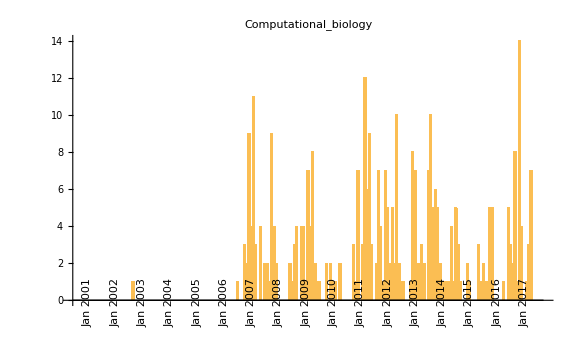
{0.456392,-Graphics-}

```mathematica
AbsoluteTiming[EditDatesPlot["Computational_biology"]]
```